Krzysztof Barczak

# Wybrane metody modelowania matematycznego

## Projekt 1

## Kod programu

Program w sposób przybliżony znajduje rozwiązanie zagadniania 
	{y''+py'+qy=f(x),
y(a)=y_a, y(b)=y_b.
Wejście:
	f - funkcja f(x),
	p, q - współczynniki równania,
	a, b - odpowiednio lewy i prawy koniec przedziału [a, b],
	ya, yb - wartości funkcji y=y(x) w końcach przedziału [a, b],
	n - ilość punktów siatki.

```mathematica
Clear[rrr2];
rrr2[f_,p_,q_,a_,b_,ya_,yb_,n_]:=Module[{h=(b-a)/(n-1),coefs,w1,w2,w3,w4,A,B,solution,iksy,dsolve,punkty,bledy,yDSolve},
w1=2-p h;
w2=2(q h^2-2);
w3=2+p h;
w4=Table[2h^2*f[x],{x,a,b,h}];
coefs=Table[i,j+1 w1+i,j w2+i,j-1 w3+j,n (w4[[i]]-i,2 ya w1-i,n-1 yb w3)-i,n-1 n,j w3,{i,2,n-1},{j,2,n}];
A=coefs[[1;;n-2,1;;n-2]];
B=coefs[[All,n-1]];
solution=LinearSolve[A,B];
solution=Prepend[Append[solution,yb],ya];
iksy=Table[a+(i-1)*h,{i,1,n}];
punkty=Transpose[{iksy,solution}];

dsolve=DSolve[{y''[x]+p*y'[x]+q y[x]==f[x],y[a]==ya,y[b]==yb},y[x],x][[1,1,2]];
(* Wartości uzyskane z DSolve w węzłach siatki *)
yDSolve=Table[dsolve/.{x->xw},{xw,a,b,(b-a)/(n-1)}];
bledy=Table[{punkty[[i,1]],Abs[punkty[[i,2]]-yDSolve[[i]]]},{i,1,n}];

Return[{Show[Plot[dsolve,{x,0,3},PlotLegends->{"DSolve"},PlotStyle->LightPurple],ListPlot[punkty,PlotStyle->Orange,PlotRange->{{.95,3.1},{0.9,2.2}},PlotMarkers->{✶,Large},PlotLegends->{"RK3"}]],ListPlot[bledy,(*Joined->True,*)PlotLegends->{"Błędy"},PlotStyle->{Thickness[.005]}]}];
]
```

## Testowanie

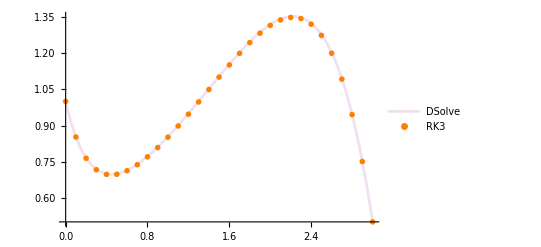

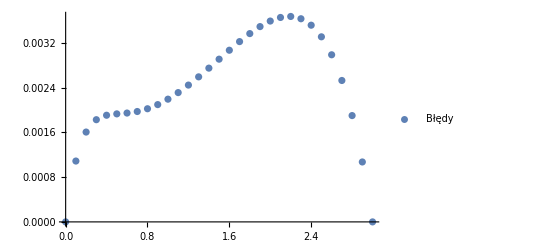

```mathematica
Clear[f,p,q,a,b,ya,yb,n];
f[x_]:=x-Exp[x];
p=3;
q=-4;
a=0;
b=3;
ya=1;
yb=.5;
n=31;
obrazki=rrr2[f,p,q,a,b,ya,yb,n];
obrazki[[1]]
obrazki[[2]]
```